```mathematica
Table[Sum[4^i,{i,0,n}],{n,0,10}]
```

{1,5,21,85,341,1365,5461,21845,87381,349525,1398101}

```mathematica
Table[1/3 (4^(n+1)-1),{n,0,10}]
```

{1,5,21,85,341,1365,5461,21845,87381,349525,1398101}

```mathematica
Simplify[Sum[4^i,{i,0,n}]==1/3 (4^(n+1)-1)]
```

True

```mathematica
all7=GenerateAllGraphsOfSize[7];
```

```mathematica
Length[all7]
```

1866256

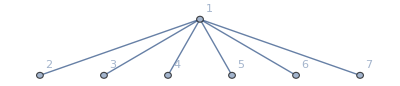
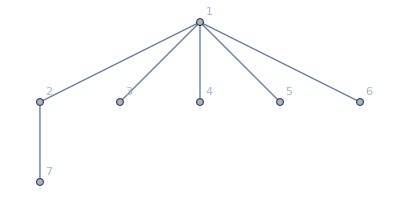
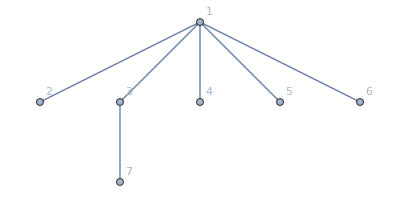
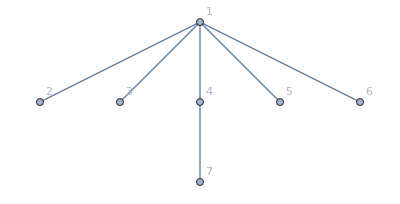
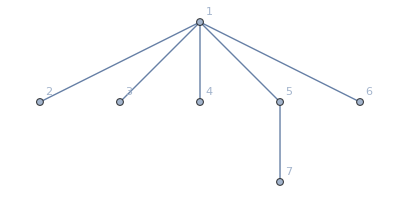

```mathematica
Take[all7,5]
```

```mathematica
min7=Select[all7,VertexCount[#]==7&&ChromaticPolynomial[#,4]==24&];
```

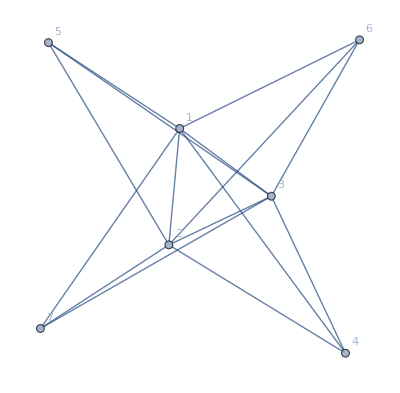
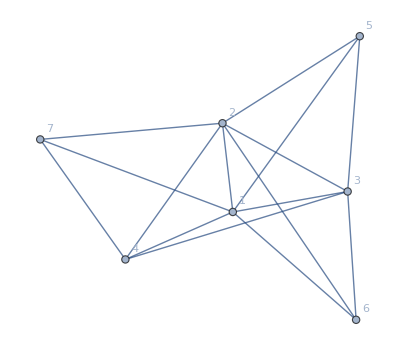
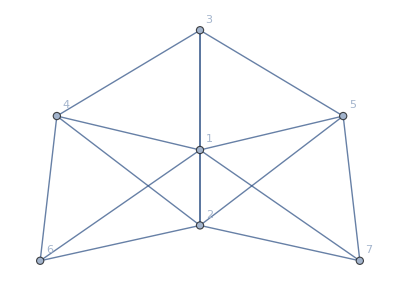
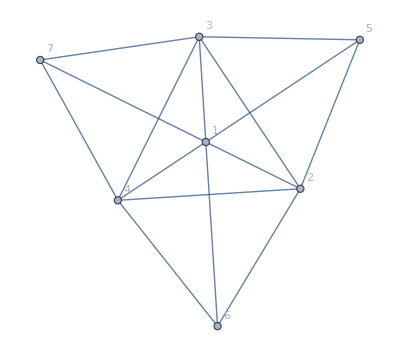
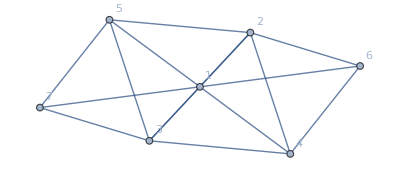
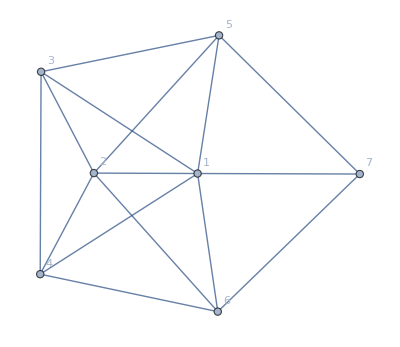
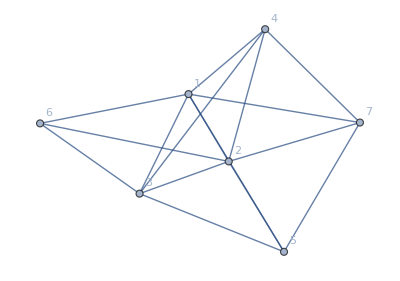
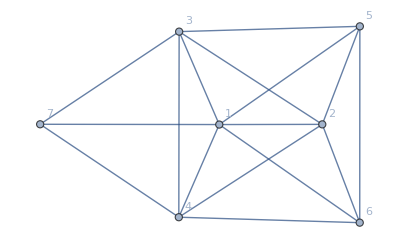
{{-Graphics-,35},{-Graphics-,1260},{-Graphics-,1260},{-Graphics-,840},{-Graphics-,2520},{-Graphics-,2520},{-Graphics-,1260},{-Graphics-,2520},{-Graphics-,2520},{-Graphics-,210},{-Graphics-,1260},{-Graphics-,105}}

```mathematica
min7Uniq=Tally[min7,IsomorphicGraphQ]
```

```mathematica
Length[min7Uniq]
```

12

```mathematica
IntegerPartitions[7,4]//Length
```

11

```mathematica
ChromaticPolynomial[-Graphics-,4]
```

24

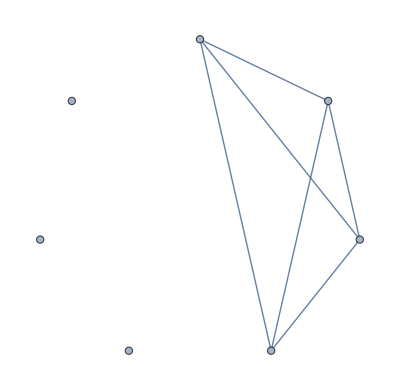
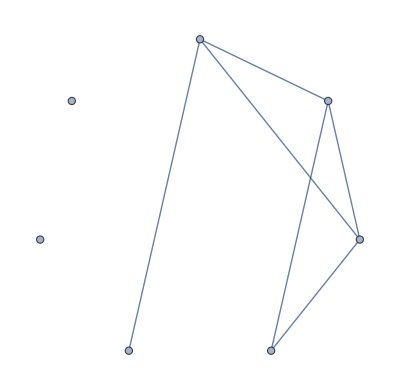
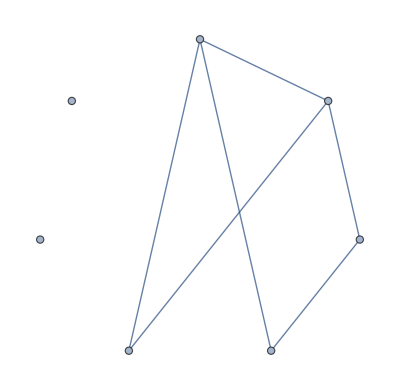
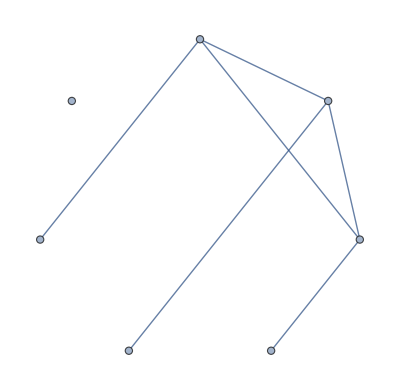
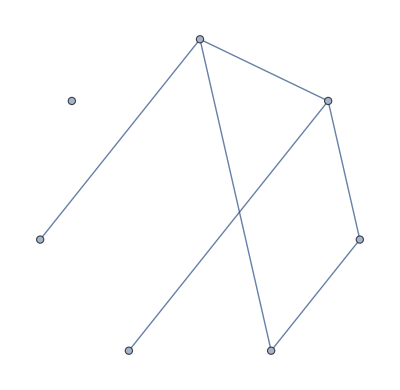
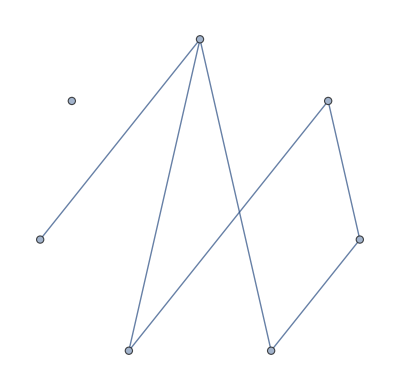
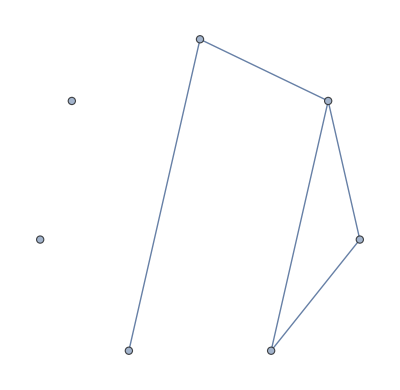
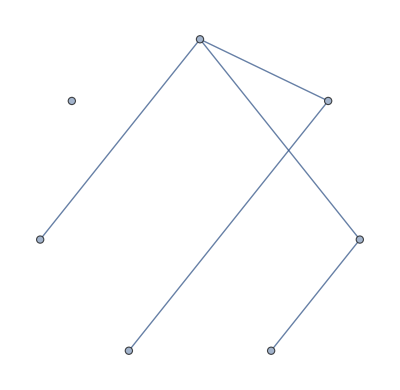
{{-Graphics-,960},{-Graphics-,960},{-Graphics-,960},{-Graphics-,960},{-Graphics-,960},{-Graphics-,1080},{-Graphics-,720},{-Graphics-,720},{-Graphics-,840},{-Graphics-,600},{-Graphics-,600},{-Graphics-,480}}

```mathematica
Map[{GraphComplement[#[[1]]],ChromaticPolynomial[#[[1]],5]}&,min7Uniq]
```

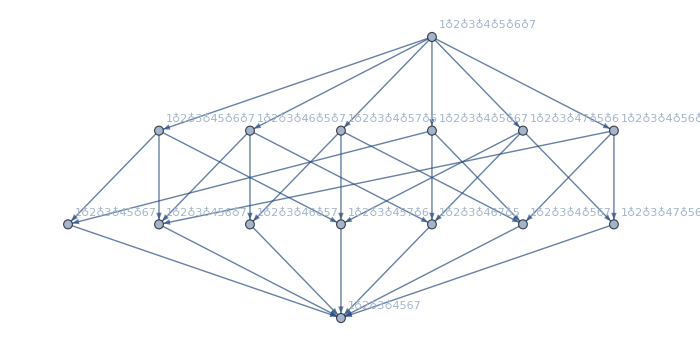
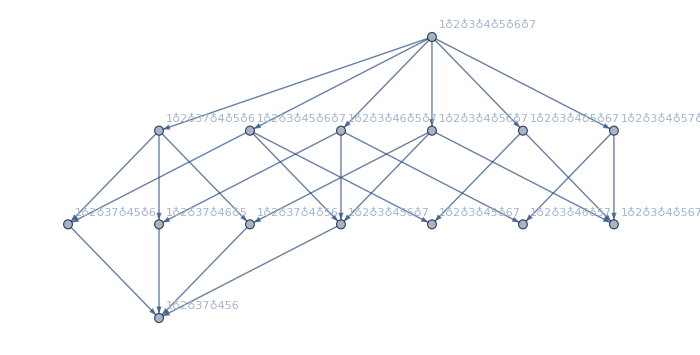
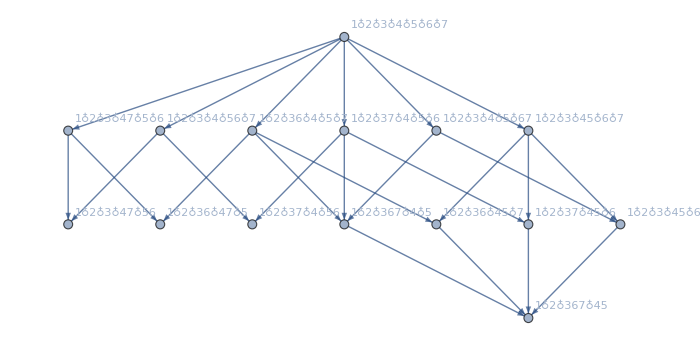
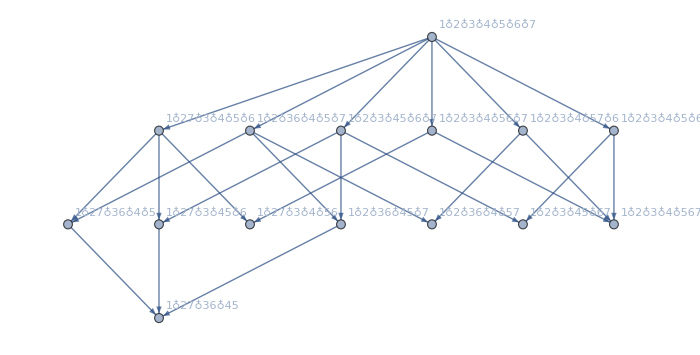
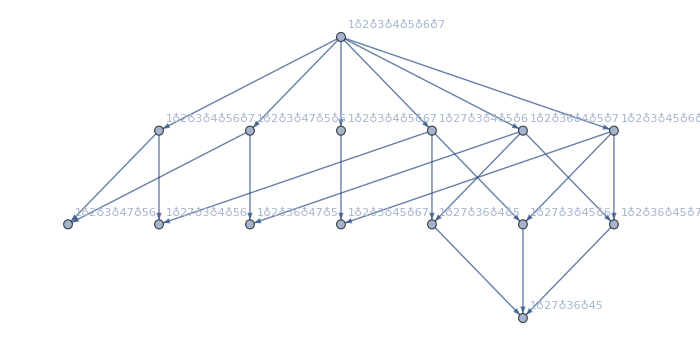
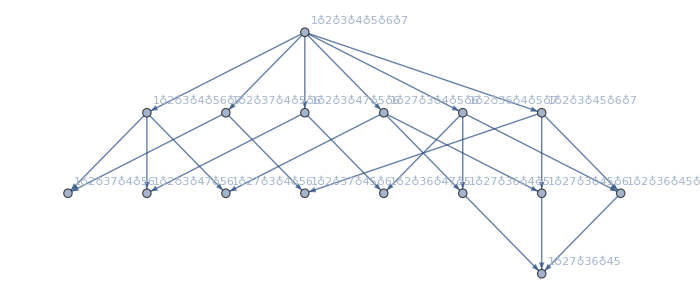
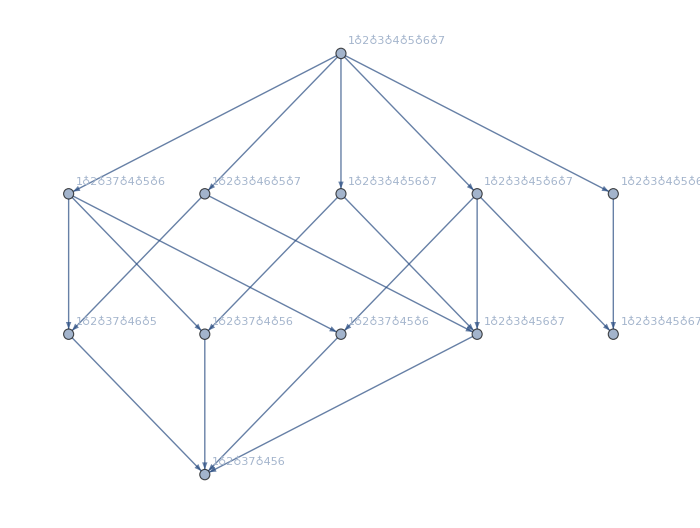
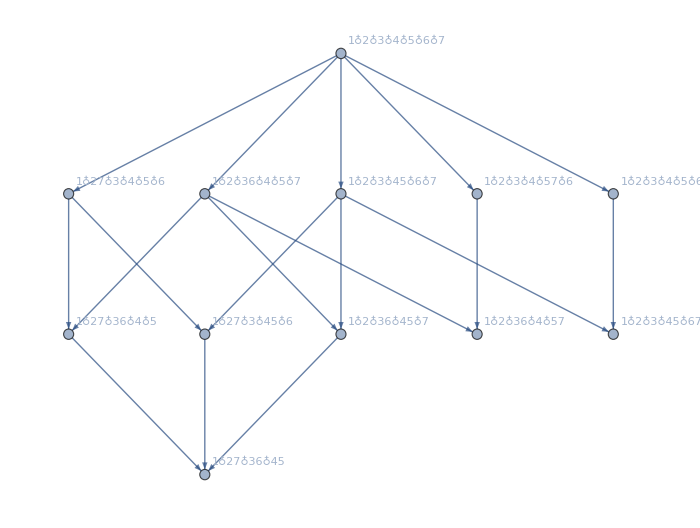
{{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-}}

```mathematica
Map[{GraphComplement[#[[1]]],Graph[FormulaGraph[ FindFullFormula[#[[1]]]],ImageSize->700]}&,min7Uniq]
```